```mathematica
(* Michael Barile 
MATH 68500
Problem #5, section 3.5
10/11/17 *)

(* Defining a function to interpolate, restricting domain to [0,1], so a=0, b=1] *)
f[x_]:=x*Sin[x]+Exp[x^2];
fprime[x_]=D[f[x],x];
a=0; b=1;

(* Defining Hermite cubic polynomials and derivatives *)
```

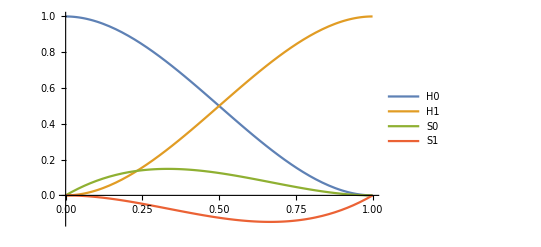

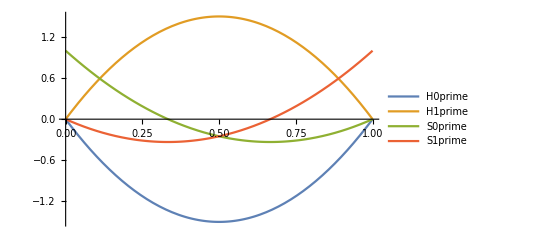

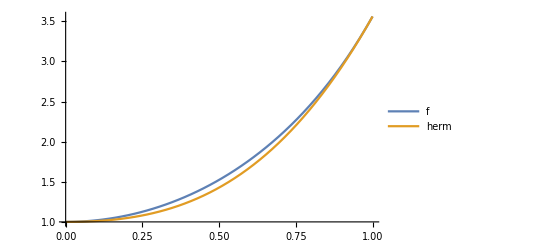

```mathematica
H0[x_]:=3*((b-x)/(b-a))^2-2*((b-x)/(b-a))^3;
H1[x_]:=3*((x-a)/(b-a))^2-2*((x-a)/(b-a))^3;
S0[x_]:=(b-x)^2/(b-a)-(b-x)^3/(b-a)^2;
S1[x_]:=-(x-a)^2/(b-a)+(x-a)^3/(b-a)^2;

H0prime[x_]=D[H0[x],x];
H1prime[x_]=D[H1[x],x];
S0prime[x_]=D[S0[x],x];
S1prime[x_]=D[S1[x],x];

Plot[{H0[x],H1[x],S0[x],S1[x]},{x,a,b},PlotLegends->{"H0","H1","S0","S1"}]
Plot[{H0prime[x],H1prime[x],S0prime[x],S1prime[x]},{x,a,b},PlotLegends->{"H0prime","H1prime","S0prime","S1prime"}]
herm[x_]:=f[a]*H0[x]+f[b]*H1[x]+fprime[a]*S0[x]+fprime[b]*S1[x];
Plot[{f[x],herm[x]},{x,a,b},PlotLegends->{"f","herm"}]

(* We see from the graphs that H0[0]=1, H0[1]=0, H1[0]= 0, H1[1]=1, S0[0]=S0[1]=S1[0]=S1[1]=0, as expected *)

(* We see that H0prime[0]=H0prime[1]=H1prime[0]=H1prime[1]=0, and S0prime[0]=1, S0prime[1]=0, S1prime[0]=0 and S1prime[1]=1, as expected. *)

(* Lastly, a plot of f against the Hermite Interpolation *)
```